```mathematica
f[m_,x_]:=Re[HankelH1[m,x]]
fperiod[m_,x_,x0_]:=If[x<x0,f[m,x],-f[m,2x0-x]]
p[m_]:=Plot[f[m,x],{x,101,102}]
pperiod[m_,x0_]:=Plot[fperiod[m,x,x0],{x,0,2x0}]
r[m_,x0_]:=FindRoot[f[m,x],{x,x0}]
```

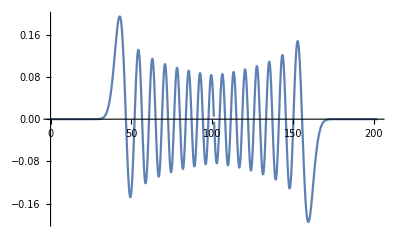

```mathematica
pperiod[40,101.15520937701599]
```

```mathematica
r[40,100]
```

{x→101.155}

```mathematica
101.15520937701599
```

```mathematica
data=Cases[Plot[fperiod[40,x,101.15520937701599],{x,0,202}],Line[data_]:>data,-4,1][[1]];
```

```mathematica
%93
```

{{{4.12878×10^-6,4.78676×10^-276},1048,{101.091,21}},1}
 |  |  |  |

```mathematica
Export["Desktop/Numerik1/hw5/fdataHW5fs19.dat",data,"Table"]
```

Desktop/Numerik1/hw5/fdataHW5fs19.dat

```mathematica
ExpandFileName["/Desktop/Numerik1/hw5/fdataHW5fs19.dat"]
```

/Desktop/Numerik1/hw5/fdataHW5fs19.dat

```mathematica
SystemOpen["fdataHW5fs19.dat"]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["fdataHW5fs19.dat"]]]
```

```mathematica
SystemOpen["fdataHW5fs19.txt"]
```

```mathematica
Cases
```